```mathematica
ClearAll["Global`*"]
```

### Data

```mathematica
max=4.0;
dx= 0.05;
xpts=281;
ypts=281;

t0=0.01;
dt=0.5;

xmin=-dx*(xpts-1)/2;
xmax=dx*(xpts-1)/2;

s1=1 + xpts * (ypts-1)/2 ;
s2=s1+xpts-1;

wd=SetDirectory@NotebookDirectory[];

hydroPath=wd<>"/../../output";
gubserPath=wd<>"/../../semi_analytic";
```

0.0105

3.01

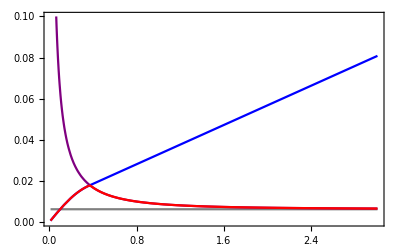

```mathematica
dtCFL = Import[hydroPath<>"/dt_CFL.dat"];
dtAdapt = Interpolation[Import[hydroPath<>"/dt_adaptive.dat"],InterpolationOrder->1];
dtSource= Interpolation[Import[hydroPath<>"/dt_source.dat"],InterpolationOrder->1];

t0CFL = dtCFL[[1,1]]
tfCFL=dtCFL[[-1,1]]
dtCFL=Interpolation[dtCFL,InterpolationOrder->1];
purple={Blend[{Blue,Purple},0.75],AbsoluteThickness[1.5]};
gray={Gray,AbsoluteThickness[1.5]};

Plot[{dx/8,dtCFL[t],dtSource[t],dtAdapt[t]},{t,t0CFL,tfCFL},PlotRange->{{t0CFL,tfCFL},{0.0001,0.1}},PlotStyle->{Gray,Purple,Blue,Red},Frame->True,FrameStyle->Black,BaseStyle->12]
```

```mathematica
t0str =NumberForm[t0,{3,3}]//ToString;
t1str=NumberForm[t0+1*dt,{3,3}]//ToString;
t2str=NumberForm[t0+2*dt,{3,3}]//ToString;
t3str=NumberForm[t0+3*dt,{3,3}]//ToString;
t4str=NumberForm[t0+4*dt,{3,3}]//ToString;
t5str=NumberForm[t0+5*dt,{3,3}]//ToString;
t6str=NumberForm[t0+6*dt,{3,3}]//ToString;
```

```mathematica
e0=Take[Import[hydroPath<>"/e_"<>t0str<>".dat"]][[All,{1,2,4}]];
e1=Take[Import[hydroPath<>"/e_"<>t1str<>".dat"]][[All,{1,2,4}]];
e2=Take[Import[hydroPath<>"/e_"<>t2str<>".dat"]][[All,{1,2,4}]];
e3=Take[Import[hydroPath<>"/e_"<>t3str<>".dat"]][[All,{1,2,4}]];
e4=Take[Import[hydroPath<>"/e_"<>t4str<>".dat"]][[All,{1,2,4}]];
e5=Take[Import[hydroPath<>"/e_"<>t5str<>".dat"]][[All,{1,2,4}]];
e6=Take[Import[hydroPath<>"/e_"<>t6str<>".dat"]][[All,{1,2,4}]];

plpt0slice=Take[Import[hydroPath<>"/plpt_"<>t0str<>".dat"]][[s1;;s2,{1,4}]];
plpt1slice=Take[Import[hydroPath<>"/plpt_"<>t1str<>".dat"]][[s1;;s2,{1,4}]];
plpt2slice=Take[Import[hydroPath<>"/plpt_"<>t2str<>".dat"]][[s1;;s2,{1,4}]];
plpt3slice=Take[Import[hydroPath<>"/plpt_"<>t3str<>".dat"]][[s1;;s2,{1,4}]];
plpt4slice=Take[Import[hydroPath<>"/plpt_"<>t4str<>".dat"]][[s1;;s2,{1,4}]];
plpt5slice=Take[Import[hydroPath<>"/plpt_"<>t5str<>".dat"]][[s1;;s2,{1,4}]];
plpt6slice=Take[Import[hydroPath<>"/plpt_"<>t6str<>".dat"]][[s1;;s2,{1,4}]];

ux0slice=Take[Import[hydroPath<>"/ux_"<>t0str<>".dat"]][[s1;;s2,{1,4}]];
ux1slice=Take[Import[hydroPath<>"/ux_"<>t1str<>".dat"]][[s1;;s2,{1,4}]];
ux2slice=Take[Import[hydroPath<>"/ux_"<>t2str<>".dat"]][[s1;;s2,{1,4}]];
ux3slice=Take[Import[hydroPath<>"/ux_"<>t3str<>".dat"]][[s1;;s2,{1,4}]];
ux4slice=Take[Import[hydroPath<>"/ux_"<>t4str<>".dat"]][[s1;;s2,{1,4}]];
ux5slice=Take[Import[hydroPath<>"/ux_"<>t5str<>".dat"]][[s1;;s2,{1,4}]];
ux6slice=Take[Import[hydroPath<>"/ux_"<>t6str<>".dat"]][[s1;;s2,{1,4}]];

ur0=Take[Import[hydroPath<>"/ur_"<>t0str<>".dat"]][[All,{1,2,4}]];
ur1=Take[Import[hydroPath<>"/ur_"<>t1str<>".dat"]][[All,{1,2,4}]];
ur2=Take[Import[hydroPath<>"/ur_"<>t2str<>".dat"]][[All,{1,2,4}]];
ur3=Take[Import[hydroPath<>"/ur_"<>t3str<>".dat"]][[All,{1,2,4}]];
ur4=Take[Import[hydroPath<>"/ur_"<>t4str<>".dat"]][[All,{1,2,4}]];
ur5=Take[Import[hydroPath<>"/ur_"<>t5str<>".dat"]][[All,{1,2,4}]];
ur6=Take[Import[hydroPath<>"/ur_"<>t6str<>".dat"]][[All,{1,2,4}]];
```

```mathematica
(* Gubser solution *)
q=1.0;
κ[τ_,r_]:=ArcTanh[(2.0*q^2*τ*r)/(1.0+q^2*(τ^2+r^2))];
ux[τ_,r_]:=Sinh[κ[τ,r]];

e0test=Take[Import[gubserPath<>"/e_gubser_"<>t0str<>".dat"]];
e1test=Take[Import[gubserPath<>"/e_gubser_"<>t1str<>".dat"]];
e2test=Take[Import[gubserPath<>"/e_gubser_"<>t2str<>".dat"]];
e3test=Take[Import[gubserPath<>"/e_gubser_"<>t3str<>".dat"]];
e4test=Take[Import[gubserPath<>"/e_gubser_"<>t4str<>".dat"]];
e5test=Take[Import[gubserPath<>"/e_gubser_"<>t5str<>".dat"]];
e6test=Take[Import[gubserPath<>"/e_gubser_"<>t6str<>".dat"]];

plpt0test=Take[Import[gubserPath<>"/plpt_ratio_gubser_"<>t0str<>".dat"]];
plpt1test=Take[Import[gubserPath<>"/plpt_ratio_gubser_"<>t1str<>".dat"]];
plpt2test=Take[Import[gubserPath<>"/plpt_ratio_gubser_"<>t2str<>".dat"]];
plpt3test=Take[Import[gubserPath<>"/plpt_ratio_gubser_"<>t3str<>".dat"]];
plpt4test=Take[Import[gubserPath<>"/plpt_ratio_gubser_"<>t4str<>".dat"]];
plpt5test=Take[Import[gubserPath<>"/plpt_ratio_gubser_"<>t5str<>".dat"]];
plpt6test=Take[Import[gubserPath<>"/plpt_ratio_gubser_"<>t6str<>".dat"]];

ux0test=Table[{xmin+i*dx,ux[t0,xmin+i*dx]},{i,0,xpts-1}];
ux1test=Table[{xmin +i*dx,ux[t0+dt,xmin+i*dx]},{i,0,xpts-1}];
ux2test=Table[{xmin +i*dx,ux[t0+2*dt,xmin+i*dx]},{i,0,xpts-1}];
ux3test=Table[{xmin +i*dx,ux[t0+3*dt,xmin+i*dx]},{i,0,xpts-1}];
ux4test=Table[{xmin +i*dx,ux[t0+4*dt,xmin+i*dx]},{i,0,xpts-1}];
ux5test=Table[{xmin +i*dx,ux[t0+5*dt,xmin+i*dx]},{i,0,xpts-1}];
ux6test=Table[{xmin +i*dx,ux[t0+6*dt,xmin+i*dx]},{i,0,xpts-1}];

(*****************************************)

e0slice=e0[[s1;;s2,{1,3}]];
e1slice=e1[[s1;;s2,{1,3}]];
e2slice=e2[[s1;;s2,{1,3}]];
e3slice=e3[[s1;;s2,{1,3}]];
e4slice=e4[[s1;;s2,{1,3}]];
e5slice=e5[[s1;;s2,{1,3}]];
e6slice=e6[[s1;;s2,{1,3}]];

(*****************************************)

Ratio1=Table[{xmin+i*dx,1.0},{i,0,xpts-1}];

de0=e0slice;
de1=e1slice;
de2=e2slice;
de3=e3slice;
de4=e4slice;
de5=e5slice;
de6=e6slice;

de0[[All,2]]/=e0test[[All,2]];
de1[[All,2]]/=e1test[[All,2]];
de2[[All,2]]/=e2test[[All,2]];
de3[[All,2]]/=e3test[[All,2]];
de4[[All,2]]/=e4test[[All,2]];
de5[[All,2]]/=e5test[[All,2]];
de6[[All,2]]/=e6test[[All,2]];

dux0=ux0slice;
dux1=ux1slice;
dux2=ux2slice;
dux3=ux3slice;
dux4=ux4slice;
dux5=ux5slice;
dux6=ux6slice;

dux0[[All,2]]/=ux0test[[All,2]];
dux1[[All,2]]/=ux1test[[All,2]];
dux2[[All,2]]/=ux2test[[All,2]];
dux3[[All,2]]/=ux3test[[All,2]];
dux4[[All,2]]/=ux4test[[All,2]];
dux5[[All,2]]/=ux5test[[All,2]];
dux6[[All,2]]/=ux6test[[All,2]];

dux0[[1+(xpts-1)/2,2]]=1.0;
dux1[[1+(xpts-1)/2,2]]=1.0;
dux2[[1+(xpts-1)/2,2]]=1.0;
dux3[[1+(xpts-1)/2,2]]=1.0;
dux4[[1+(xpts-1)/2,2]]=1.0;
dux5[[1+(xpts-1)/2,2]]=1.0;
dux6[[1+(xpts-1)/2,2]]=1.0;

dplpt0=plpt0slice;
dplpt1=plpt1slice;
dplpt2=plpt2slice;
dplpt3=plpt3slice;
dplpt4=plpt4slice;
dplpt5=plpt5slice;
dplpt6=plpt6slice;

dplpt0[[All,2]]/=plpt0test[[All,2]];
dplpt1[[All,2]]/=plpt1test[[All,2]];
dplpt2[[All,2]]/=plpt2test[[All,2]];
dplpt3[[All,2]]/=plpt3test[[All,2]];
dplpt4[[All,2]]/=plpt4test[[All,2]];
dplpt5[[All,2]]/=plpt5test[[All,2]];
dplpt6[[All,2]]/=plpt6test[[All,2]];
```

Divide::indet: Indeterminate expression 0./0. encountered.

### Colors and Labels

```mathematica
colors={Darker[Blue],Blue,Cyan, Green,Yellow,Orange ,Red,Darker[Red]};
colorpts=Table[1.0*i/(Length[colors]-1),{i,0,Length[colors]-1}];

Unprotect[ColorData];
ColorData["Energy"]=Function[x,Blend[Transpose[{colorpts,colors}],x ]];
ColorData["Flow"]=Function[x,Blend[Transpose[{colorpts,colors}],x / max]];
Protect[ColorData];

Grid[{{BarLegend[{ColorData["Energy"],{0,1}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}],
BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->300,LabelStyle->{FontSize->13,FontFamily->"Arial",Black}]}}];

magentaTran={Blend[{Red,Magenta},0.5],AbsoluteThickness[2],Opacity[0.3]};
redTran={Red,AbsoluteThickness[2],Opacity[0.3]};
orangeTran={Blend[{Red,Orange},0.75],AbsoluteThickness[2],Opacity[0.3]};
greenTran={Blend[{Blue,Green},0.875],AbsoluteThickness[2],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[2],Opacity[0.3]};
cyanTran={Blend[{Blue,Cyan},0.75],AbsoluteThickness[2],Opacity[0.3]};
blueTran={Blue,AbsoluteThickness[2],Opacity[0.3]};
purpleTran={Blend[{Blue,Purple},0.75],AbsoluteThickness[2],Opacity[0.3]};

magenta={Blend[{Red,Magenta},0.5],AbsoluteDashing[{8,6}],AbsoluteThickness[2]};
red={Red,AbsoluteDashing[{8,6}],AbsoluteThickness[2]};
orange={Blend[{Red,Orange},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[2]};
green={Blend[{Blue,Green},0.875],AbsoluteDashing[{8,6}],AbsoluteThickness[2]};
cyan={Blend[{Blue,Cyan},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[2]};
blue={Blue,AbsoluteDashing[{8,6}],AbsoluteThickness[2]};
purple={Blend[{Blue,Purple},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[2]};

magentaSolid={Blend[{Red,Magenta},0.5],AbsoluteThickness[1.5]};
redSolid={Red,AbsoluteThickness[1.5]};
orangeSolid={Blend[{Red,Orange},0.75],AbsoluteThickness[1.5]};
greenSolid={Blend[{Blue,Green},0.875],AbsoluteThickness[1.5]};
cyanSolid={Blend[{Blue,Cyan},0.75],AbsoluteThickness[1.5]};
blueSolid={Blue,AbsoluteThickness[1.5]};
purpleSolid={Blend[{Blue,Purple},0.75],AbsoluteThickness[1.5]};
blackSolid={Black,AbsoluteThickness[1.5]};

style={magentaTran,redTran,orangeTran,greenTran,cyanTran,blueTran,purpleTran,magenta,red,orange,green,cyan, blue,purple};
styleSolid={blackSolid,magentaSolid,redSolid,orangeSolid,greenSolid,cyanSolid, blueSolid,purpleSolid};




(* Plot Labels *)
eLabel=Panel[Grid[{{Style["ℰ",FontSize->18,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
uxLabel=Panel[Grid[{{Style["u_x",FontSize->18,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
plptLabel=Panel[Grid[{{Style["(P_(L_((<>)_(<>))))/(P_⊥)",FontSize->22,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
eRatioLabel=Panel[Grid[{{Style["(ℰ_((<>)_(<>)))/ℰ_exact",FontSize->22,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
uxRatioLabel=Panel[Grid[{{Style["(u_(x_((<>)_(<>))))/(u_(x, exact))",FontSize->22,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
plptRatioLabel=Panel[Grid[{{Style["(P_(L_((<>)_(<>))))/((SubscriptBox[P, L]/SubscriptBox[P, ⊥])_exact)",FontSize->22,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];

size=25;

(*legendTimes1=Panel[Grid[{{Graphics[{Directive[Blend[{Red,Magenta},0.5],AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.25],Style["τ = 0.25 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Red,AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.25],Style["τ = 0.75 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Red,Orange},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.25],Style["τ = 1.25 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Blue,Green},0.875],AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.25],Style["τ = 1.75 fm/c",FontSize->12.75,FontFamily->"Arial"]}}],Background->White,FrameMargins->0]


legendTimes2=Panel[Grid[{{Graphics[{Directive[Blend[{Blue,Cyan},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.25],Style["τ = 2.25 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blue,AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.25],Style["τ = 2.75 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Blue,Purple},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.25],Style["τ = 3.25 fm/c",FontSize->12.75,FontFamily->"Arial"]}}],Background->White,FrameMargins->0]
*)
legendTimes3=Grid[{{Graphics[{Directive[Blend[{Red,Magenta},0.5],AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 0.01 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Red,AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 0.51 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Red,Orange},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 1.01 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Blue,Green},0.875],AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 1.51 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Blue,Cyan},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 2.01 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blue,AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 2.51 fm/c",FontSize->12.75,FontFamily->"Arial"]},
{Graphics[{Directive[Blend[{Blue,Purple},0.75],AbsoluteDashing[{8,6}],AbsoluteThickness[2]],Line[{{0,0},{1,0}}]},ImageSize->size,AspectRatio->0.3],Style["τ = 3.01 fm/c",FontSize->12.75,FontFamily->"Arial"]}
}];



initTime1=Grid[{{Style["  τ_0 = 0.01 fm/c",FontSize->13,FontFamily->"Arial"]},
{Style["ρ_0 = -5.3169",FontSize->13,FontFamily->"Arial"]}}]

initTime2=Grid[{{Style["  τ_0 = 0.01 fm/c",FontSize->13,FontFamily->"Arial"]},
{Style["ρ_0 = -5.9808",FontSize->13,FontFamily->"Arial"]}}]

initEta=Style["η_(<>)/_(<>)s = 0.2",FontSize->13,FontFamily->"Arial"];

timeresLabel1=Style["Δτ = 0.005 fm_(<>)/_(<>)c",FontSize->13,FontFamily->"Arial"];

spaceresLabel1=Grid[{
{Style["Δx = 0.05 fm",FontSize->13,FontFamily->"Arial"]},
{Style["Δy = 0.05 fm",FontSize->13,FontFamily->"Arial"]}}];

timeresLabel2=Style["Δτ = 0.001 fm_(<>)/_(<>)c",FontSize->13,FontFamily->"Arial"];

spaceresLabel2=Grid[{
{Style["Δx = 0.01 fm",FontSize->13,FontFamily->"Arial"]},
{Style["Δy = 0.01 fm",FontSize->13,FontFamily->"Arial"]}}];

gridLabel1=Style["Grid: 7 fm × 7 fm",FontSize->13,FontFamily->"Arial"];
gridLabel2=Style["Grid: 7 fm × 7 fm",FontSize->13,FontFamily->"Arial"];
ThetaLabel=Style["Θ_flux = 1.8",FontSize->14,FontFamily->"Arial"];

plptHat=Style["(P̂)_L0/(P̂)_(⊥0) = 10^-3",FontSize->13,FontFamily->"Arial"];

rhoLabel1=Style["(T̂)_0 = 0.04296",FontSize->13,FontFamily->"Arial"];

rhoLabel2=Style["(T̂)_0 = 0.02614",FontSize->13,FontFamily->"Arial"];
```

τ_0 = 0.01 fm/c
ρ_0 = -5.3169

τ_0 = 0.01 fm/c
ρ_0 = -5.9808

### Ticks

```mathematica
min = {0.009,0};
maj={0.016,0};

logticks = {{0.001,"10^-3",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"0.01",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},
{0.1,"0.1",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},
{1,"1",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},
{10,"10",maj},{20,"",min},{30,"",min},{40,"",min},{50,"",min},{60,"",min},{70,"",min},{80,"",min},{90,"",min},
{100,"100",maj},{200,"",min},{300,"",min},{400,"",min},{500,"",min},{600,"",min},{700,"",min},{800,"",min},{900,"",min},
{1000,"10^3",maj},{2000,"",min},{3000,"",min},{4000,"",min},{5000,"",min},{6000,"",min},{7000,"",min},{8000,"",min},{9000,"",min},{10000,"10^4",maj},{20000,"",min}};

nologticks =  {{0.001,"",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},
{0.1,"",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},
{1,"",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},
{10,"",maj},{20,"",min},{30,"",min},{40,"",min},{50,"",min},{60,"",min},{70,"",min},{80,"",min},{90,"",min},
{100,"",maj},{200,"",min},{300,"",min},{400,"",min},{500,"",min},{600,"",min},{700,"",min},{800,"",min},{900,"",min},
{1000,"",maj},{2000,"",min},{3000,"",min},{4000,"",min},{5000,"",min},{6000,"",min},{7000,"",min},{8000,"",min},{9000,"",min},{10000,"",maj},{20000,"",min}};


xticks = {{-5,"-5",maj},{-4.75,"",min},{-4.5,"",min},{-4.25,"",min},
{-4,"-4",maj},{-3.75,"",min},{-3.5,"",min},{-3.25,"",min},
{-3,"-3",maj},{-2.75,"",min},{-2.5,"",min},{-2.25,"",min},
{-2,"-2",maj},{-1.75,"",min},{-1.5,"",min},{-1.25,"",min},
{-1,"-1",maj},{-0.75,"",min},{-0.5,"",min},{-0.25,"",min},
{0,"0",maj},{0.25,"",min},{0.5,"",min},{0.75,"",min},
{1,"1",maj},{1.25,"",min},{1.5,"",min},{1.75,"",min},
{2,"2",maj},{2.25,"",min},{2.5,"",min},{2.75,"",min},
{3,"3",maj},{3.25,"",min},{3.5,"",min},{3.75,"",min},
{4,"4",maj},{4.25,"",min},{4.5,"",min},{4.75,"",min},{5,"5",maj}};

noxticks = {{-5,"",maj},{-4.75,"",min},{-4.5,"",min},{-4.25,"",min},
{-4,"",maj},{-3.75,"",min},{-3.5,"",min},{-3.25,"",min},
{-3,"",maj},{-2.75,"",min},{-2.5,"",min},{-2.25,"",min},
{-2,"",maj},{-1.75,"",min},{-1.5,"",min},{-1.25,"",min},
{-1,"",maj},{-0.75,"",min},{-0.5,"",min},{-0.25,"",min},
{0,"",maj},{0.25,"",min},{0.5,"",min},{0.75,"",min},
{1,"",maj},{1.25,"",min},{1.5,"",min},{1.75,"",min},
{2,"",maj},{2.25,"",min},{2.5,"",min},{2.75,"",min},
{3,"",maj},{3.25,"",min},{3.5,"",min},{3.75,"",min},
{4,"",maj},{4.25,"",min},{4.5,"",min},{4.75,"",min},{5,"",maj}};

ratioticks = {{0.95,"0.95",maj},{0.96,"",min},{0.97,"",min},{0.98,"",min},{0.99,"",min},{1,"1.0",maj},
{1.01,"",min},{1.02,"",min},{1.03,"",min},{1.04,"",min},{1.05,"1.05",maj}};

noratioticks = {{0.95,"",maj},{0.96,"",min},{0.97,"",min},{0.98,"",min},{0.99,"",min},{1,"",maj},
{1.01,"",min},{1.02,"",min},{1.03,"",min},{1.04,"",min},{1.05,"",maj}};
```

### Plots

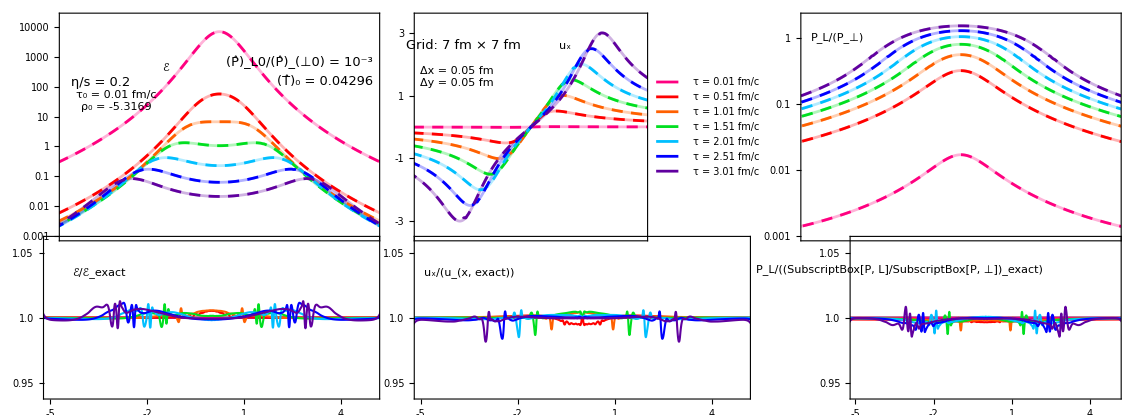
-Graphics-x (fm)

```mathematica
image=400;

(* Image Padding *)
a=30;
b=30;
c=15;
d=0;

Panel[GraphicsGrid[{
{ListLogPlot[{e0test,e1test,e2test,e3test,e4test,e5test,e6test,e0slice,e1slice,e2slice,e3slice,e4slice,e5slice,e6slice},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.001,2*10^4}},PlotStyle->style,Frame->True,FrameTicks->{{logticks,nologticks},{noxticks,noxticks}},FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImagePadding->{{a,b},{c,d}},Epilog->{Inset[eLabel,{-1.75,6}],Inset[initTime1,{-3.35,3.5}],Inset[initEta,{-3.875,4.9}],Inset[rhoLabel1,{3.425,5}],Inset[plptHat,{2.6,6.5}]},ImageSize->image],

ListPlot[{ux0test,ux1test,ux2test,ux3test,ux4test,ux5test,ux6test,ux0slice,ux1slice,ux2slice,ux3slice,ux4slice,ux5slice,ux6slice},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{-3.5,3.5}},PlotStyle->style,Frame->True,FrameTicks->{{xticks, noxticks},{noxticks,noxticks}},FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImagePadding->{{a,b},{c,d}},Epilog->{Inset[uxLabel,{1.5,2.6}],Inset[gridLabel1,{-3,2.6}],Inset[spaceresLabel1,{-3.3,1.6}],Inset[legendTimes3,{2.5,-1.7}]},ImageSize->image],

ListLogPlot[{plpt0test,plpt1test,plpt2test,plpt3test,plpt4test,plpt5test,plpt6test,plpt0slice,plpt1slice,plpt2slice,plpt3slice,plpt4slice,plpt5slice,plpt6slice},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.001,2.0}},PlotStyle->style,Frame->True,FrameTicks->{{logticks,nologticks},{noxticks,noxticks}},FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImagePadding->{{a,b},{c,d}},Epilog->Inset[plptLabel,{-4,0.0}],ImageSize->image]},


{ListPlot[{Ratio1,de0,de1,de2,de3,de4,de5,de6},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.94,1.06}},PlotStyle->styleSolid,Frame->True,FrameStyle->Black,FrameTicks->{{ratioticks,noratioticks},{xticks,noxticks}},Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.5,ImagePadding->{{a,b},{c,d}},Epilog->{Inset[eRatioLabel,{-3.5,1.035}]},ImageSize->image],

ListPlot[{Ratio1,dux0,dux1,dux2,dux3,dux4,dux5,dux6},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.94,1.06}},PlotStyle->styleSolid,Frame->True,FrameTicks->{{ratioticks,noratioticks},{xticks,noxticks}},FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.5,ImagePadding->{{a,b},{c,d}},Epilog->{Inset[uxRatioLabel,{-3.5,1.035}]},ImageSize->image],

ListPlot[{Ratio1,dplpt0,dplpt1,dplpt2,dplpt3,dplpt4,dplpt5,dplpt6},Joined->True,InterpolationOrder->2,PlotRange->{{-5,5},{0.94,1.06}},PlotStyle->styleSolid,Frame->True,FrameTicks->{{ratioticks,noratioticks},{xticks,noxticks}},FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.5,ImagePadding->{{a,b},{c,d}},Epilog->{Inset[plptRatioLabel,{-3.3,1.037}]},ImageSize->image]}

},

Spacings->{-25,-78.5}],

{Style["x (fm)",FontFamily->"Arial",FontSize->18]},{{Bottom,Center}},Appearance->"Frameless",FrameMargins->0,Background->White]

Export[wd<>"/gubser_aniso_test_fully_adaptive.pdf",%];
```

```mathematica
tcolor=Black;

s ={0.01125,0.01125};
l={0.02,0.02};

(*xaxisL={{-5,"-5",l,Black},
{-4.5,"",s,tcolor},{-4,"-4",l,tcolor},{-3.5,"",s,tcolor},{-3,"-3",l,tcolor},{-2.5,"",s,tcolor},
{-2,"-2",l,tcolor},{-1.5,"",s,tcolor},{-1,"-1",l,tcolor},{-0.5,"",s,tcolor},{0,"0",l,tcolor},
{0.5,"",s,tcolor},{1,"1",l,tcolor},{1.5,"",s,tcolor},{2,"2",l,tcolor},{2.5,"",s,tcolor},
{3,"3",l,tcolor},{3.5,"",s,tcolor},{4,"4",l,tcolor},{4.5,"",s,tcolor},{5,"5",l,Black}};*)

xaxis={{-4.5,"",s,tcolor},{-4,"",l,tcolor},{-3.5,"",s,tcolor},{-3,"",l,tcolor},{-2.5,"",s,tcolor},
{-2,"",l,tcolor},{-1.5,"",s,tcolor},{-1,"",l,tcolor},{-0.5,"",s,tcolor},{0,"0",l,tcolor},
{0.5,"",s,tcolor},{1,"",l,tcolor},{1.5,"",s,tcolor},{2,"",l,tcolor},{2.5,"",s,tcolor},
{3,"",l,tcolor},{3.5,"",s,tcolor},{4,"",l,tcolor},{4.5,"",s,tcolor},{5,"5",l,tcolor}};

xaxisnone={{-4.5,"",s,tcolor},{-4,"",l,tcolor},{-3.5,"",s,tcolor},{-3,"",l,tcolor},{-2.5,"",s,tcolor},
{-2,"",l,tcolor},{-1.5,"",s,tcolor},{-1,"",l,tcolor},{-0.5,"",s,tcolor},{0,"",l,tcolor},
{0.5,"",s,tcolor},{1,"",l,tcolor},{1.5,"",s,tcolor},{2,"",l,tcolor},{2.5,"",s,tcolor},
{3,"",l,tcolor},{3.5,"",s,tcolor},{4,"",l,tcolor},{4.5,"",s,tcolor},{5,"",l,tcolor}};

xaxisAll={{-5,"-5",l,tcolor},{-4.5,"",s,tcolor},{-4,"",l,tcolor},{-3.5,"",s,tcolor},{-3,"",l,tcolor},{-2.5,"",s,tcolor},
{-2,"",l,tcolor},{-1.5,"",s,tcolor},{-1,"",l,tcolor},{-0.5,"",s,tcolor},{0,"0",l,tcolor},
{0.5,"",s,tcolor},{1,"",l,tcolor},{1.5,"",s,tcolor},{2,"",l,tcolor},{2.5,"",s,tcolor},
{3,"",l,tcolor},{3.5,"",s,tcolor},{4,"",l,tcolor},{4.5,"",s,tcolor},{5,"5",l,tcolor}};


Max[e2[[All,3]]]
Max[e4[[All,3]]]
Max[e6[[All,3]]]
```

18.6343

1.79053

0.499792

```mathematica
a=25;
r=6.5;
s=4.5;
u=9.5;
(*{a,a},{a,a};
{Automatic,Automatic},{Automatic,Automatic};*)

x=-60;

e0plot=ListDensityPlot[e0,PlotRange->{{-5,5},{-5,5},{0,1350}},PlotRangePadding->None,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,1350}},LegendMarkerSize->225,LegendMargins->{{0,0},{0,0}},LabelStyle->{FontSize->12,FontFamily->"Arial",Black}],Left],ColorFunction->ColorData["Energy"],Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{{"",""},{"",""}},FrameTicks->{{xaxis,xaxisnone},{xaxisnone,xaxisAll}},BaseStyle->13,ImagePadding->{{a,a},{a,a}},ImageSize->300];

ur0plot=ListDensityPlot[ur0,PlotRange->{{-5,5},{-5,5},{0,max}},PlotRangePadding->None,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LegendMargins->{{u,u},{0,0}},LabelStyle->{FontSize->12,FontFamily->"Arial",Black}],Right],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{{"",""},{"",""}},FrameTicks->{{xaxisnone,xaxis},{xaxisnone,xaxis}},BaseStyle->13,ImagePadding->{{a,a},{a,a}},ImageSize->300];


e2plot=ListDensityPlot[e2,PlotRange->{{-5,5},{-5,5},{0,20}},PlotRangePadding->None,(*BoundaryStyle->Directive[White,AbsoluteThickness[2]],*)PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,20}},LegendMarkerSize->225,LegendMargins->{{r,r},{0,0}},LabelStyle->{FontSize->12,FontFamily->"Arial",Black}],Left],ColorFunction->ColorData["Energy"],Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{{"",""},{"",""}},FrameTicks->{{xaxis,xaxisnone},{xaxisnone,xaxisnone}},BaseStyle->13,ImageSize->300,ImagePadding->{{a,a},{a,a}}];

ur2plot=ListDensityPlot[ur2,PlotRange->{{-5,5},{-5,5},{0,max}},PlotRangePadding->None,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LegendMargins->{{u,u},{0,0}},LabelStyle->{FontSize->12,FontFamily->"Arial",Black}],Right],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{{"",""},{"",""}},FrameTicks->{{xaxisnone,xaxis},{xaxisnone,xaxisnone}},BaseStyle->13,ImageSize->300,ImagePadding->{{a,a},{a,a}}];

e4plot=ListDensityPlot[e4,PlotRange->{{-5,5},{-5,5},{0,2}},PlotRangePadding->None,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,2}},LegendMarkerSize->225,LegendMargins->{{s,s},{0,0}},LabelStyle->{FontSize->12,FontFamily->"Arial",Black}],Left],ColorFunction->ColorData["Energy"],Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{{"",""},{"",""}},FrameTicks->{{xaxis,xaxisnone},{xaxisnone,xaxisnone}},BaseStyle->13,ImageSize->300,ImagePadding->{{a,a},{a,a}}];

ur4plot=ListDensityPlot[ur4,PlotRange->{{-5,5},{-5,5},{0,max}},PlotRangePadding->None,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LegendMargins->{{u,u},{0,0}},LabelStyle->{FontSize->12,FontFamily->"Arial",Black}],Right],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{{"",""},{"",""}},FrameTicks->{{xaxisnone,xaxis},{xaxisnone,xaxisnone}},BaseStyle->13,ImageSize->300,ImagePadding->{{a,a},{a,a}}];

e6plot=ListDensityPlot[e6,PlotRange->{{-5,5},{-5,5},{0,0.5}},PlotRangePadding->None,PlotLegends->Placed[BarLegend[{ColorData["Energy"],{0,0.5}},LegendMarkerSize->225,LegendMargins->{{s,s},{0,0}},LabelStyle->{FontSize->12,FontFamily->"Arial",Black}],Left],ColorFunction->ColorData["Energy"],Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{{"",""},{"",""}},FrameTicks->{{xaxisAll,xaxisnone},{xaxisAll,xaxisnone}},BaseStyle->13,ImageSize->300,ImagePadding->{{a,a},{a,a}}];

ur6plot=ListDensityPlot[ur6,PlotRange->{{-5,5},{-5,5},{0,max}},PlotRangePadding->None,PlotLegends->Placed[BarLegend[{ColorData["Flow"],{0,max}},LegendMarkerSize->225,LegendMargins->{{u,u},{0,0}},LabelStyle->{FontSize->12,FontFamily->"Arial",Black}],Right],ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,Frame->True,Axes->False,FrameStyle->Black,FrameLabel->{{"",""},{"",""}},FrameTicks->{{xaxisnone,xaxisAll},{xaxis,xaxisnone}},BaseStyle->13,ImageSize->300,ImagePadding->{{a,a},{a,a}}];
```

```mathematica
Panel[GraphicsGrid[{{e0plot, ur0plot},{e2plot,ur2plot},{e4plot,ur4plot},{e6plot,ur6plot}},
ImageSize->{UpTo[700],UpTo[1250]},Spacings->{-74.8,-128.6}],

{Style["x (fm)",FontFamily->"Arial",FontSize->16],Style["y (fm)",FontFamily->"Arial",FontSize->16]},{{Bottom,Center},{Left,Center}},Appearance->"Frameless",FrameMargins->0,Background->White];

Export[wd<>"/gubser_aniso_2d_test_CFL_adaptive.png",%];
```

```mathematica
-105.5/-49.1*x
```

-128.921

```mathematica
r=6.0;
s=4.4;
u=9.6;

Grid[{{BarLegend[{ColorData["Energy"],{0,1350}},LegendMarkerSize->225,LegendMargins->{{0,0},{0,0}},LegendFunction->(Framed[#,FrameMargins->0]&),LabelStyle->{FontSize->12,FontFamily->"Arial",Black}]},
{BarLegend[{ColorData["Flow"],{0,4}},LegendMarkerSize->225,LegendMargins->{{u,u},{0,0}},LegendFunction->(Framed[#,FrameMargins->0]&),LabelStyle->{FontSize->12,FontFamily->"Arial",Black}]},
{BarLegend[{ColorData["Energy"],{0,20}},LegendMarkerSize->225,LegendMargins->{{r,r},{0,0}},LegendFunction->(Framed[#,FrameMargins->0]&),LabelStyle->{FontSize->12,FontFamily->"Arial",Black}]},
{BarLegend[{ColorData["Energy"],{0,2}},LegendMarkerSize->225,LegendMargins->{{s,s},{0,0}},LegendFunction->(Framed[#,FrameMargins->0]&),LabelStyle->{FontSize->12,FontFamily->"Arial",Black}]},
{BarLegend[{ColorData["Energy"],{0,0.5}},LegendMarkerSize->225,LegendMargins->{{s,s},{0,0}},LegendFunction->(Framed[#,FrameMargins->0]&),LabelStyle->{FontSize->12,FontFamily->"Arial",Black}]}}]

Export[wd<>"/legends.pdf",%];
```

```mathematica
Grid[{{ListContourPlot[e6,PlotRange->{{-5,5},{-5,5},{0,0.5}},Contours->15,ColorFunction->ColorData["Energy"],FrameStyle->Black,BaseStyle->14,ImageSize->400],

ListContourPlot[ur6,PlotRange->{{-5,5},{-5,5},{0,4}},Contours->15,ColorFunction->ColorData["Flow"],ColorFunctionScaling->False,FrameStyle->Black,BaseStyle->14,ImageSize->400]}}];

Export[wd<>"/gubser_aniso_contour_CFL_fully_adaptive.png",%];
```

```mathematica
Max[e6[[All,3]]]
```

0.488173